```mathematica
Array[f,3];
```

```mathematica
f[1]=Import["/home/runbo/Desktop/Summer_Research/CS2010-188-1051"];
f[2]=Import["/home/runbo/Desktop/Summer_Research/CS2010-200-1312"];
f[3]=Import["/home/runbo/Desktop/Summer_Research/CS2010-208-1328"];
```

```mathematica
Array[n, 3];
```

```mathematica
n[1]=NonlinearModelFit[f[1], a x^b, {a, b}, x]
n[2]=NonlinearModelFit[f[2], a x^b, {a, b}, x]
n[3]=NonlinearModelFit[f[3], a x^b, {a, b}, x]
```

FittedModel[0.135457/x^0.910135]

FittedModel[0.119765 x^0.148642]

FittedModel[0.186478/x^0.542563]

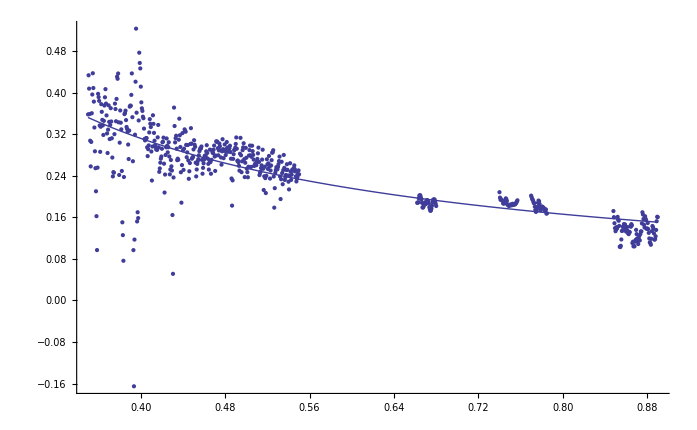

```mathematica
Show[ListPlot[f[1]], Plot[n[1][x], {x, 0.35, 0.89}]]
```

```mathematica
Array[p, 3];
```

```mathematica
p[1]=n[1]["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
a | 0.135457 | 0.00349165 | {0.128599,0.142315}
b | -0.910135 | 0.0325171 | {-0.973999,-0.846271}

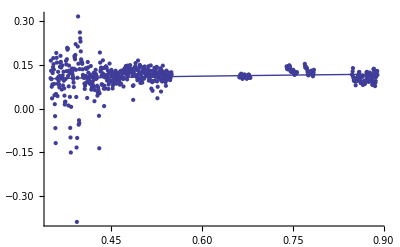

| Estimate | Standard Error | Confidence Interval
a | 0.119765 | 0.0048082 | {0.110322,0.129208}
b | 0.148642 | 0.0600162 | {0.030769,0.266514}

```mathematica
Show[ListPlot[f[2]], Plot[n[2][x], {x, 0.35, 0.89}]]
p[2]=n[2]["ParameterConfidenceIntervalTable"]
```

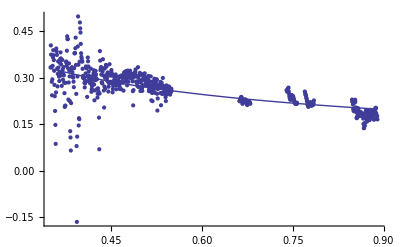

| Estimate | Standard Error | Confidence Interval
a | 0.186478 | 0.00396525 | {0.17869,0.194266}
b | -0.542563 | 0.0281032 | {-0.597758,-0.487368}

```mathematica
Show[ListPlot[f[3]], Plot[n[3][x], {x, 0.35, 0.89}]]
p[3]=n[3]["ParameterConfidenceIntervalTable"]
```